# Chapter 5 Fitting Data to Nonlinear Models

One of the most difficult topics in all of data analysis in the physical sciences is fitting data to nonlinear models. Often such fits require large computational resources and great skill, patience, and intuition on the part of the analyst. These difficulties are one of the reasons that, as we shall see, the whole topic of spectral line shapes is still a very active subject of research spanning the fields of chemistry, physics, astronomy, and more. In addition, computational methods of nonlinear fitting are still a current research topic in computer science.

However, since sometimes nature really is nonlinear, such fits are often unavoidable, and the principles and some tools for nonlinear fitting are the topics of this chapter. The main EDA program introduced here is EDAFindFit, which accomplishes fits to arbitrary models.

EDAFindFit is similar to the NonlinearFit function in the Statistics`NonlinearFit` package which is standard with Mathematica. The primary differences are that EDAFindFit: (1) recognizes EDA’s data format, including errors in both coordinates; (2) estimates errors in fit parameters; (3) by default displays graphical information about the fit; and (4) uses an algorithm that has been optimized for speed and stability for the types of nonlinear fits commonly performed in the physical sciences and engineering.

## 5.1 Introduction

### 5.1.1 Overview of EDAFindFit

The previous chapter, “Fitting Data to Linear Models by Least-Squares Techniques,” introduced the distinction between linear and nonlinear models. To briefly review, the terms refer to the way in which the parameters to which we are fitting enter into the model.

In this chapter we discuss nonlinear models and the EDA program EDAFindFit that can often find a reasonable fit to them.

Recall that if sos is the sum of the squares of the residuals, then we are seeking the minimum in its value. If we are fitting to parameters a[0], a[1], ... , a[m], the answer is found by solving a set of simultaneous equations.

```mathematica
D[sos, a[0]] == 0
D[sos, a[1]] == 0
...
D[sos, a[m]] == 0
```

This, in general, can be done analytically, provided the model to which we are fitting is linear in the parameters. Similarly, when there are explicit errors in the data, we form the chi-squared, χ^2, and we solve the corresponding equations.

```mathematica
D[χ^2, a[0]] == 0
D[χ^2, a[1]] == 0
...
D[χ^2, a[m]] == 0
```

This again will be analytic for a linear fit.

For a nonlinear fit, no such analytic solutions are possible, so iteration is required to find the minimum in the sum of the squares or the chi-squared.

If we imagine a plot of the value of the sum of the squares or the chi-squared as a function of the parameters to which we are fitting, in general for a nonlinear fit there may be many local minima instead of one big one, as is the case for linear fitting. For example, if we are fitting to two parameters, param1 and param2, the chi-squared as a function of the values of the parameters might have two or more local minima.

```mathematica
Plot3D[1-1/(param1^2+param2^2+35)-1/((param1-25)^2+(param2+10)^2+25),{param1,-20,50},{param2,-25,25},PlotRange->All,PlotPoints->40,Ticks->{Automatic,Automatic,None},AxesLabel->{"param1","param2","chi-squared"},ViewPoint->{1.3,2.4,0.75}]
```

-Graphics3D-

Thus, a nonlinear fitter must usually start off with initial values close to the real minimum.

The general technique for iteration, “steepest descent,” is analogous to the following situation. “It was a dark and stormy night.” Foggy too. You are on the side of a hill and want to find the valley. So, you step in the direction in which the slope goes down, and continue moving in the direction of the local definition of “down” until you are in the valley. Of course, if you take giant steps you might step over the next hill and end up in the wrong valley. And when you get close to the bottom of the valley you will want to start taking baby steps. The Levenberg-Marquardt algorithm used by many nonlinear fitters, including EDAFindFit by default, is essentially some clever heuristics to define giant steps and baby steps.

If the data has noise, which is almost a certainty for real experimental data, then there is a further difficulty. We can take two sets of data from the same apparatus using the same sample, fit each dataset to a nonlinear model using identical initial values for the fit parameters, and get very different final fits. This situation leads to ambiguity about which fit results are “correct.”

### 5.1.2 Providing Initial Parameter Values to EDAFindFit

As already mentioned, unless we are fitting to a very simple model, EDAFindFit must be provided with initial estimates of the parameters.

We will first fit to a simple model where no such parameter estimates are necessary.

```mathematica
Needs["EDA`"]
```

```mathematica
mydata=Table[{n,2 Cos[3 n]},{n,0.,1.5,.5}];
```

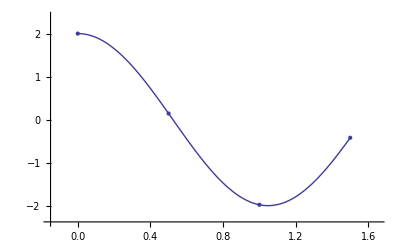

{a→{3.,0.32},b→{2.,0.7},SumOfSquares→8.3348×10^-22,DegreesOfFreedom→2}

```mathematica
EDAFindFit[mydata,b Cos[a x],x,{a,b}]
```

Actually, when not given initial values EDAFindFit starts with initial values for the parameters, here a and b, equal to 1.

Now the syntax of the call to EDAFindFit is given.

```mathematica
EDAFindFit[data,model,ind,{param1,...,paramM} ]
```

Here ind is the name of the independent variable in model. Also note that this model is nonlinear in the parameters to which we are fitting, param1 ... paramM.

The EDA`FindFit` package includes a Gaussian function.

```mathematica
?Gaussian
```

Gaussian[x, ampl, x0, sigma] is a Gaussian function of the independent
	variable x with amplitude ampl, center value x0, and standard
	deviation sigma. The function is normalized so that its integral
	from -Infinity to +Infinity is equal to Sqrt[2Pi]*ampl*sigma.

We will use it to generate some data.

```mathematica
SeedRandom[1234];
mydata=Table[{x,Gaussian[x,1000,400,100]+RandomReal[{-1,1}]},{x,1,1000}];
```

We examine the data with EDAListPlot.

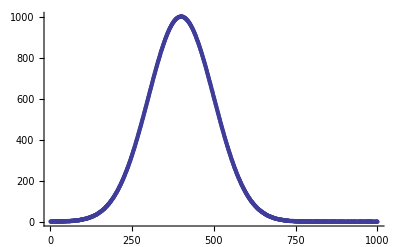

```mathematica
EDAListPlot[mydata]
```

We fit the data using EDAFindFit; the fit takes a few seconds to complete.

```mathematica
EDAFindFit[mydata,Gaussian[x,ampl,x0,sigma],x,{ampl,x0,sigma}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 30 iterations.

$Failed

As discussed above, EDAFindFit must iterate to a solution. We can increase the maximum number of iterations with an option.

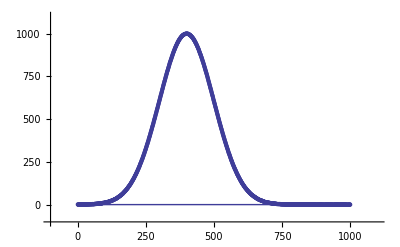

{ampl→{3.7491,0.002},x0→{1.43,0.16},sigma→{0.27,0.1},SumOfSquares→1.77272×10^8,DegreesOfFreedom→997}

```mathematica
EDAFindFit[mydata,Gaussian[x,ampl,x0,sigma],x,{ampl,x0,sigma}, MaximumIterations -> 50]
```

This result is ridiculous. What has happened is that EDAFindFit thinks it has found a local minimum in the sum of the squares at these silly values.

Repeating the fit with reasonable initial guesses of the parameters gives a much better result.

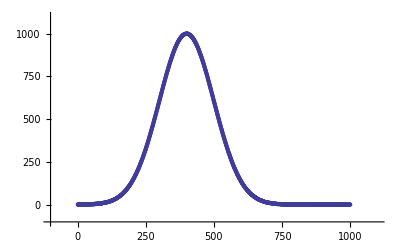

{ampl→{1000.03,0.092},x0→{400.003,0.011},sigma→{100.008,0.011},SumOfSquares→345.609,DegreesOfFreedom→997}

```mathematica
EDAFindFit[mydata,Gaussian[x,ampl,x0,sigma],x,{{ampl,900},{x0,350},{sigma,120}}]
```

Finding good initial values is sometimes subtle. As an example, we generate some made-up data for three peaks with a Lorentzian shape using the Lorentzian function supplied with the EDA`FindFit` package.

Lorentzian[x, a, x0, gamma] is a nonrelativistic Lorentzian
	function of the independent variable x, center value x0, and full
	width at half-maximum gamma. The function is normalized
	so that its integral from -Infinity to +Infinity is equal to 
	"a". The maximum amplitude of the peak is 2*a/(Pi*gamma). Lorentzian
	is a synonym for BreitWigner.

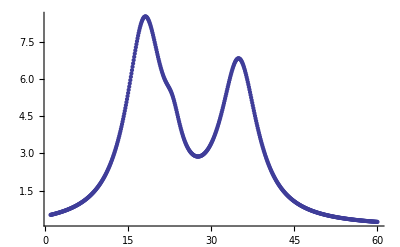

```mathematica
? Lorentzian
mydata=Table[{x,Lorentzian[x,100,18,8]+Lorentzian[x,10,23,4]+Lorentzian[x,80,35,8]},{x,1,60,.1}];
EDAListPlot[mydata]
```

It is difficult to see the small peak on the shoulder of the leftmost peak, or to provide initial estimates for its values. However, we can see the peak and probably make some sensible guesses of its parameters.

Despite the claims sometimes seen in glossy advertisements, there is no known software that can find and estimate peaks for data such as this as well as a human expert. This is in part because of the great ability of the human visual system to be an intuitive integrator.

Almost all versions of the notebook front end for Mathematica include a provision to use our visual ability. We can display a graph of the data and use the mouse to point to a desired location on the graph; for Windows versions we must hold down the Ctrl key. The coordinates will be displayed in the notebook window, and can also be copied out using the cut-and-paste facility; consult the manual for your version of the notebook to discover how to do this. For example, here we load and examine a part of a nuclear spectrum.

```mathematica
LoadData[Cobalt60]
```

LoadData::name: Loading: Cobalt60Data

```mathematica
?Cobalt60Data
```

Cobalt60Data is part of a cobalt-60 nuclear spectrum. The
	format is: {channel, counts}. The data was collected in the second-year
	Lab of the Department of Physics, University of Toronto with a NaI 
	scintillator and a PC-based multichannel analyzer running PC-MCA software 
	by David Harrison (1990, unpublished).

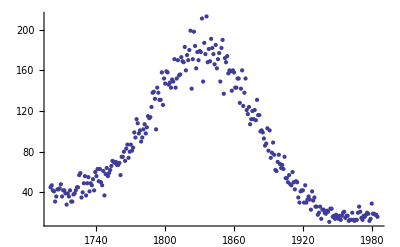

```mathematica
EDAListPlot[Cobalt60Data]
```

Using the mouse we can pick out the coordinates of the maximum, the points on the peak corresponding to roughly one-half the maximum, and so on. So, the position of the peak is found.

```mathematica
{1831.88,181.251}
```

In some earlier versions of the Windows front end, if the notebook is closed and then reopened, the coordinates will be returned in PostScript units instead of the actual units of the plot; rerendering the plot works around this bug.

Finally, for simple spectra EDA supplies a function FindPeaks, which can sometimes provide initial guesses of the number of peaks and their parameter values close enough for EDAFindFit. The function is described in Section 8.3.

### 5.1.3 Comparing LinearFit and EDAFindFit

Although EDAFindFit is intended for fitting to nonlinear models, it can also find the minimum in the sum of the squares or the chi-squared for linear models, although more slowly than LinearFit.

For example, here we repeat a fit from Chapter 4.

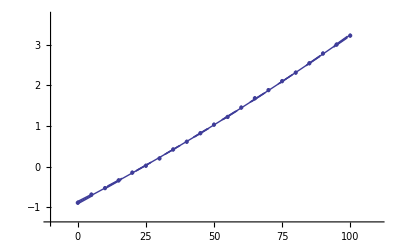

{a[0]→{-0.886,0.03},a[1]→{0.0352,0.0014},a[2]→{0.00006,0.000013},ChiSquared→1.0066,DegreesOfFreedom→18}

```mathematica
LinearFit[ThermocoupleData,{0,1,2},a]
```

Using EDAFindFit yields the same result.

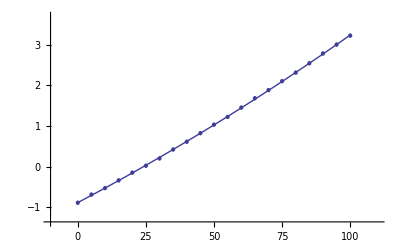

{a[0]→{-0.886,0.03},a[1]→{0.0352,0.0014},a[2]→{0.00006,0.000013},ChiSquared→1.0066,DegreesOfFreedom→18}

```mathematica
EDAFindFit[ThermocoupleData,a[0]+a[1] x+a[2] x^2,x,{a[0],a[1],a[2]}]
```

Although not an issue for this small data set, EDAFindFit took about four times as long as LinearFit.

Recall from the chapter on linear fitting that if the data have explicit errors in both coordinates, the effective variance technique makes the fit essentially nonlinear unless the model is a straight line. Thus, in this case LinearFit iterates until it finds a minimum in the chi-squared. When there are errors in both coordinates, EDAFindFit also calculates the error in the dependent variable based on the effective variance. However, although there is a fairly comprehensive literature on using this technique in linear fits, the main justification for using effective variances in nonlinear fits is based only on a series of experiments in which it was found that the algorithm of EDAFindFit would produce reasonable results most of the time.

We repeat another fit from the chapter on linear models.

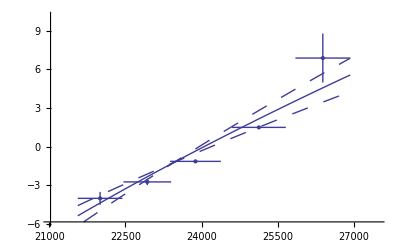

{a[-1]→{-590000.,110000.},a[1]→{0.00102,0.0002},ChiSquared→2.19143,DegreesOfFreedom→3}

```mathematica
LinearFit[ReactanceData,{-1,1},a]
```

EDAFindFit gives a similar result if started sufficiently close to the “final” values.

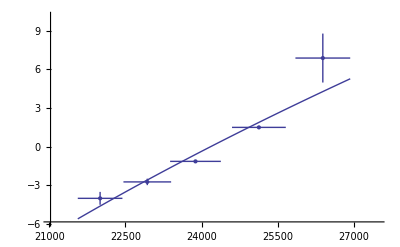

{a[-1]→{-590000.,3.8×10^-14},a[1]→{0.001009,0.000021},ChiSquared→2.20372,DegreesOfFreedom→3}

```mathematica
EDAFindFit[ReactanceData,a[-1]/x+a[1] x,x,{{a[-1],-590000},{a[1],0.001}}]
```

For the above results, EDAFindFit appears to have done a poorer job of estimating the errors in the fit parameters than LinearFit.

Another difference between the two fits above is that, by default, the graphs produced by LinearFit display the errors in the fit parameters, while the graphs produced by EDAFindFit do not. This is because for many nonlinear fits, sorting out how to combine the various error terms is problematic. To display the fit errors, the UseFitErrors option (discussed in Section 5.3.2.2) may be set to True.

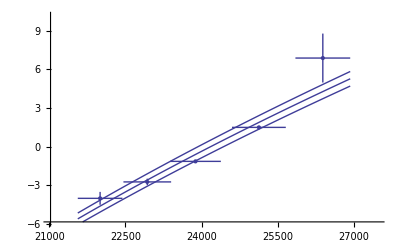

{a[-1]→{-590000.,3.8×10^-14},a[1]→{0.001009,0.000021},ChiSquared→2.20372,DegreesOfFreedom→3}

```mathematica
EDAFindFit[ReactanceData,a[-1]/x+a[1] x,x,{{a[-1],-590000},{a[1],0.001}},UseFitErrors->True]
```

Note that as opposed to the plot produced by LinearFit, here the lines representing the errors in the fit parameters are parallel. This is an artifact of a heuristic used by the EDAFindFit package to combine the two terms; the heuristic is often reasonable for true nonlinear fits.

As a final comparison between LinearFit and EDAFindFit, we load and examine some data on oscillations in interneuron networks.

```mathematica
LoadData[Interneuron]
```

LoadData::name: Loading: InterneuronData

```mathematica
?InterneuronData
```

InterneuronData is data of oscillations of interneuron networks
	driven by metabotopic glutamate receptor activation in slices of
	rat hippocampus and neocortex. The data is from Miles A.
	Whittington, Roger D. Traub, and John G.R. Jefferys, Nature 373,
	(1995) pg 612. The format of the data is {ipscTau, frequency}, where
	'ipscTau' is the decay constant of the inhibitory postsynaptic currents
	in ms and 'frequency' is the oscillation frequency of the network
	in Hz.

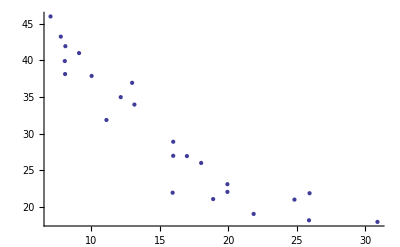

```mathematica
EDAListPlot[InterneuronData]
```

The data appears to be modeled by an exponential relationship.

```mathematica
frequency = a ⅇ^(-b * ipscTau)
```

This is nonlinear in the parameters a and b. However, as mentioned in the previous chapter, we can linearize the relationship by taking the logarithm of both sides.

```mathematica
Log[frequency] = Log[a] - b*ipscTau
```

Thus, we form a data set of {ipscTau, Log[frequency]}.

```mathematica
mydata=({First[#1],Log[Last[#1]]}&)/@InterneuronData;
```

We fit this transformed data to a straight line.

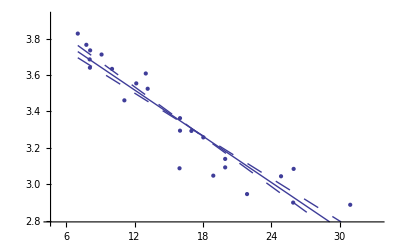

{a[0]→{4.027,0.057},a[1]→{-0.0424,0.0033},PseudoErrorY→0.107598,SumOfSquares→0.2547,DegreesOfFreedom→22}

```mathematica
linresult=LinearFit[mydata,{0,1},a]
```

Thus b = - 0.0424 ± 0.0033 in ((ms))^(-1). Although there are problems with the above fit, which are discussed below, we will calculate a and its errors using the Datum construct discussed in Chapter 3.

```mathematica
Exp[Datum[a[0]]/.linresult]/.Datum->Identity
```

{56.1,3.2}

Using EDAFindFit, we can fit directly to the exponential.

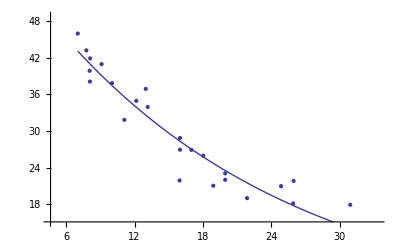

{a→{59.9,1.},b→{0.0468,0.0012},SumOfSquares→164.391,DegreesOfFreedom→22}

```mathematica
EDAFindFit[InterneuronData,a Exp[-b x],x,{{a,56},{b,-0.04}}]
```

The two fits are similar, and both show some problems in the residuals. Also, EDAFindFit seems more confident about the uncertainties in the values of the fit parameters, probably without justification. The difference in the SumOfSquares is because of the different values being used for the dependent variable of the data.

One likely reason for the problems here is that the data does not seem to asymptotically approach zero, as assumed by our model, but some other value c.

```mathematica
frequncy = a*Exp[-b*ipscTau] + c
```

Fitting to this model seems to confirm our hypothesis.

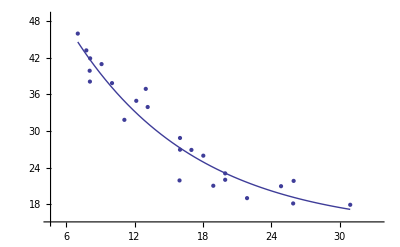

{a→{59.,2.3},b→{0.0925,0.0094},c→{13.8,1.5},SumOfSquares→132.854,DegreesOfFreedom→21}

```mathematica
EDAFindFit[InterneuronData,a Exp[-b x]+c,x,{{a,60},{b,0.05},{c,15}}]
```

This essentially duplicates a fit presented by the experimenters in their original paper.

The model can be linearized as follows.

```mathematica
frequncy = a*Exp[-b*ipscTau] + c
frequency - c = a*Exp[-b*ipscTau]
Log[frequency - c] = Log[a] - b*ipscTau
```

Thus, we can form another data set in which we subtract 13.8 from each value of frequency before taking the logarithms.

```mathematica
mydata2=({First[#1],Log[Last[#1]-13.8]}&)/@InterneuronData;
```

We fit this to a straight line.

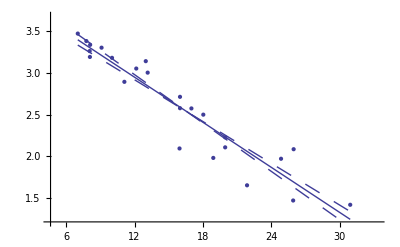

{a[0]→{4.03,0.11},a[1]→{-0.0901,0.0066},PseudoErrorY→0.215214,SumOfSquares→1.01897,DegreesOfFreedom→22}

```mathematica
linresult2=LinearFit[mydata2,{0,1},a]
```

Thus, a can be calculated.

```mathematica
Exp[Datum[a[0]/.linresult2]]/.Datum->Identity
```

{56.3,6.2}

This number is within errors of the result found by EDAFindFit.

Of course, without EDAFindFit or some other nonlinear fitter available, it would be difficult to get an objective estimate of the value that should be subtracted from each value of the dependent variable frequency.

Also, although not an issue here, this sort of linearization procedure can introduce biases in the values of the estimates of the fit parameters; this is discussed further in Chapter 8.

### 5.1.4 References

Philip R. Bevington, Data Reduction and Error Analysis (McGraw-Hill, 1969), Chapter 11. A classic introduction to nonlinear fitting techniques

Xiang Ouyang and Philip L. Varghese, Applied Optics 28 (1989), p. 1538. A discussion of a popular Fourier transform-based algorithm for fitting spectra to Galatry and Voigt profiles

William H. Press, Brian P. Flannery, Saul A. Teukolsky, and William T. Vetterling, Numerical Recipes: The Art of Scientific Computing or Numerical Recipes in C: The Art of Scientific Computing (Cambridge Univ. Press), Section 14.4. A good brief introduction to nonlinear fitting and the Levenberg-Marquardt algorithm used by EDAFindFit

A.P. De Weljer, C.B. Lucasius, L. Buydens, G. Kateman, H.M. Heuvel, and H. Mannee, Anal. Chem. 66 (1994), p. 23. An illuminating discussion of the research into fitting to curves using neural networks, this article also has a good review of some of the problems with conventional techniques

## 5.2 Examples

### 5.2.1 Fitting to a Single Peak with a Background

We begin by loading and examining some data that was briefly examined in Section 5.1.2.

```mathematica
Needs["EDA`"]
```

```mathematica
LoadData[Cobalt60]
```

LoadData::name: Loading: Cobalt60Data

```mathematica
? Cobalt60Data
```

Cobalt60Data is part of a cobalt-60 nuclear spectrum. The
	format is: {channel, counts}. The data was collected in the second-year
	Lab of the Department of Physics, University of Toronto with a NaI 
	scintillator and a PC-based multichannel analyzer running PC-MCA software 
	by David Harrison (1990, unpublished).

```mathematica
EDAListPlot[Cobalt60Data]
```

-Graphics-

The theoretical prediction for the peak is that it should be a Gaussian, so part of the model for the fit will be the Gaussian function included in the EDA`FindFit` package.

```mathematica
? Gaussian
```

Gaussian[x, ampl, x0, sigma] is a Gaussian function of the independent
	variable x with amplitude ampl, center value x0, and standard
	deviation sigma. The function is normalized so that its integral
	from -Infinity to +Infinity is equal to Sqrt[2Pi]*ampl*sigma.

We also note that there is a background under the peak, that is, counts in addition to the Gaussian peak. We will approximate the background as a straight line with the following slope.

```mathematica
a[1]=N[(16-44)/(1950-1700)]
```

-0.112

Here the numbers in the calculation are based on values obtained by pointing and clicking at the left- and right-hand sides of the plot of the data with the mouse. We calculate the intercept.

```mathematica
a[0]=16-a[1] 1950
```

234.4

From the plot of the data we estimate the center of the peak to be at channel 1830, and the amplitude above the background is about 140 counts. The full width at half-maximum is about 90 channels, so we will try an initial value for sigma of 45 channels.

Since we are going to use a[0] and a[1] as names for fit parameters, we must clear the definitions we have just made for them.

```mathematica
Remove["a*"]
```

Now we fit to the data.

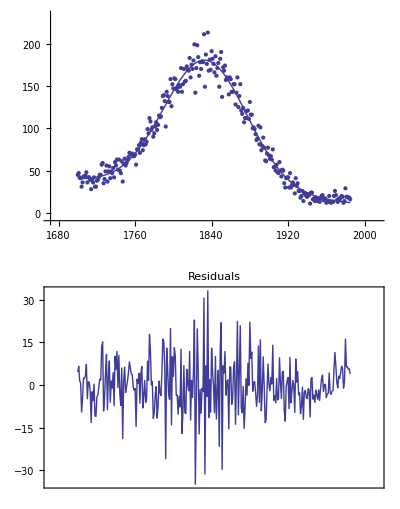

{a[0]→{201.5,1.6},a[1]→{-0.09556,0.00087},ampl→{154.03,0.17},x0→{1833.51,0.054},sigma→{43.499,0.069},SumOfSquares→23500.7,DegreesOfFreedom→281}

```mathematica
EDAFindFit[Cobalt60Data,a[0]+a[1] chan+Gaussian[chan,ampl,x0,sigma],chan,{{a[0],234},{a[1],-0.11},{ampl,140},{x0,1830},{sigma,45}}]
```

Note that the Reweight option, which is True by default for LinearFit, is False by default for EDAFindFit. Section 5.3.1.9 discusses this further.

Note also that because all four quadrants of the plot of the data and the fit contain significant amounts of data, EDAFindFit displays the plot of the residuals separately.

Here is the syntax of the call to EDAFindFit.

```mathematica
EDAFindFit[ data, model, ind, params ]
```

The model is the model to which we are fitting and ind is the independent variable. The params can be a list of the parameter names.

```mathematica
{param1, param2, ... , paramM}
```

More often params is a list of {parameter name, initial value} pairs.

```mathematica
{ {param1, value1}, {param2, value2}, ... ,
	{paramM, valueM} }
```

The world will end if model contains undefined arguments in addition to ind and those named in params.

Other forms of parameter specification include {name, min, start, max}, which causes EDAFindFit to begin parameter name at start and not allow it to go below min or above max. Or the parameter can be specified as {name, min, max}, in which case the value starts at (min + max)/2.

Note that in comparison to fits you may have done using LinearFit, EDAFindFit is very slow.

From the theory of nuclear physics, we expect the error in the number of counts in each channel to be Sqrt[counts]. Thus, we form a new data set with these errors included.

```mathematica
mydata=N[({#1⟦1⟧,{#1⟦2⟧,√(#1⟦2⟧)}}&)/@Cobalt60Data];
```

We fit to this new data set.

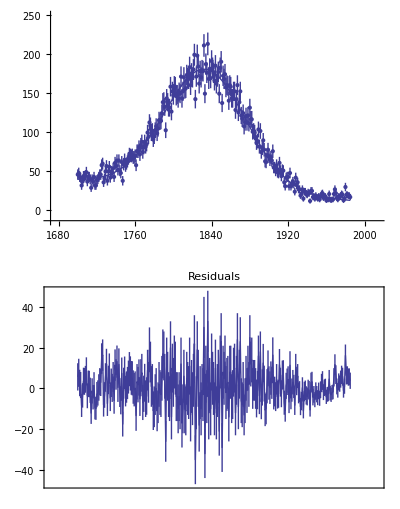

{a[0]→{194.,10.},a[1]→{-0.0919,0.0052},ampl→{154.8,1.7},x0→{1832.99,0.51},sigma→{42.89,0.55},ChiSquared→299.418,DegreesOfFreedom→281}

```mathematica
EDAFindFit[mydata,a[0]+a[1] chan+Gaussian[chan,ampl,x0,sigma],chan,{{a[0],234},{a[1],-0.11},{ampl,140},{x0,1830},{sigma,45}}]
```

Although the error bars in the data have obscured the curve representing the fit, the residuals and the ChiSquared per DegreesOfFreedom show that the fit is reasonable, except perhaps on the far right-hand side.

There is another sort of bell-shaped curve that high-energy physicists usually call a “Breit-Wigner”. The same curve is usually called a “Lorentzian” by spectroscopists. The EDA`FindFit` package includes a BreitWigner function.

```mathematica
? BreitWigner
```

BreitWigner[x, a, x0, gamma] is a nonrelativistic Breit-Wigner
	function of the independent variable x, center value x0, and full
	width at half-maximum gamma. The function is normalized
	so that its integral from -Infinity to +Infinity is equal to 
	"a". The maximum amplitude of the peak is 2*a/(Pi*gamma). BreitWigner
	is a synonym for Lorentzian.

Note that, consistent with a common convention, BreitWigner does not take the maximum amplitude as an argument, but instead the total area under the curve. If the peak in the Cobalt-60 data is a Breit-Wigner, this corresponds to the total number of counts in the peak. The total number of counts in the data, peak plus background, can be calculated.

```mathematica
Last[Plus@@Cobalt60Data]
```

24057

Also, the width is specified by the full width at the half-maximum, not the standard deviation. We fit the Cobalt-60 data with errors to a Breit-Wigner plus a linear background.

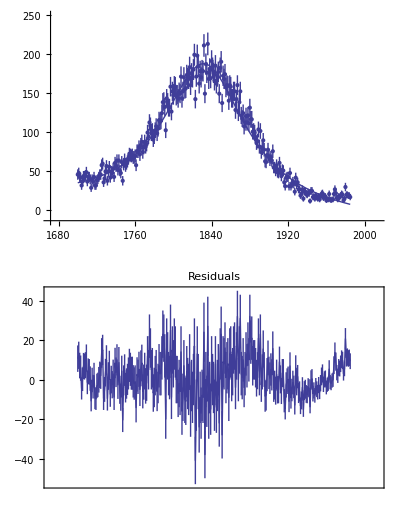

{a0→{138.,11.},a1→{-0.0764,0.0057},a→{31600.,780.},x0→{1832.08,0.55},g→{106.2,2.4},ChiSquared→448.257,DegreesOfFreedom→281}

```mathematica
EDAFindFit[mydata,a0+a1 * chan+BreitWigner[chan,a,x0,g],chan,{{a0,234},{a1,-0.11},{a,24000},{x0,1830},{g,90}}]
```

Because of the possibility that EDAFindFit fell into the wrong minimum in the chi-squared, caution must be used in rejecting the model (i.e., a Breit-Wigner plus background) because of a large ChiSquared per DegreesOfFreedom. Nonetheless, the residuals seem to be saying clearly that the data does not match a Breit-Wigner.

For the fit to a Gaussian, there are some signs of a problem at higher values of the channel. We try to account for that by adding a quadratic term to the background.

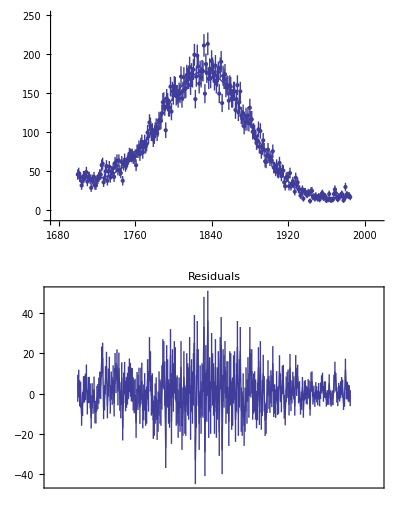

{a[0]→{5184.33,0.00065},a[1]→{-5.5549,0.0062},a[2]→{0.001487,3.2×10^-6},ampl→{179.103,0.023},x0→{1833.5,0.47},sigma→{48.25,0.56},ChiSquared→267.609,DegreesOfFreedom→280}

```mathematica
result = EDAFindFit[mydata,a[0]+a[1] chan+a[2] chan^2 +Gaussian[chan,ampl,x0,sigma],chan,{{a[0],234},{a[1],-0.11},{a[2], 0.02},{ampl,140},{x0,1830},{sigma,45}}]
```

This seems to be much better. Note that the values of the parameters for the background have changed dramatically by the addition of the second-order term.

Finally, we can compare the total number of counts in the data, 24057, to the total predicted from the fit.

```mathematica
N[NIntegrate[Gaussian[x,179.10,1833.5,48.25]+5184.28-5.555 x  + 0.001487 * x^2,{x,1700,1985}]]
```

23671.9

Whether or not this number is close to the experimental number cannot be answered until we do some error analysis.  We can find the contributions to this number from the background and the Gaussian, including errors, using some tools discussed in Chapter 3.

We ignore the quadratic term in the background. Using the Datum construct, we can find the counts and error in the counts due to the background.

```mathematica
bkgd=∫_1700^1985 (a+b x + c x^2)ⅆx/.{a->Datum[a[0]],b->Datum[a[1]], c -> Datum[a[2]]}/.result
```

2200.±4500.

We use the fact that the Gaussian is essentially zero at both the left and right of the data, so we can use the full normalization of the Gaussian to calculate the counts under the peak.

```mathematica
peak=N[√(2 π)] Datum[ampl] Datum[sigma]/.result
```

21650.±250.

Thus, the total number of counts predicted by the fit is calculated.

```mathematica
bkgd+peak
```

23800.±4500.

This compares well with the experimental value of 24057.

### 5.2.2 Fitting to Three Peaks with No Background

A common line shape in the study of infrared absorption and emission is called a Galatry profile. The EDA`FindFit` package includes a function for this shape.

```mathematica
? Galatry
```

Galatry[y, z, tau] is a Galatry profile with collision broadening
	parameter "y", collision narrowing parameter "z", and dimensionless
	time "tau". The profile is normalized so that its value is one
	when tau = 0.

We will use this function to generate some made-up data of three Galatry peaks.

```mathematica
SeedRandom[1234];
mydata=Table[{t,2 Galatry[0.95,1.,t-5]+1.3 Galatry[1.3,1.,t-12]+1.2 Galatry[0.9,1.,t-25]+RandomReal[{-0.07,0.07}]},{t,0,35,0.2}];
```

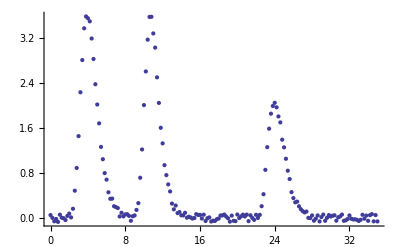

```mathematica
EDAListPlot[mydata]
```

We fit to this data.

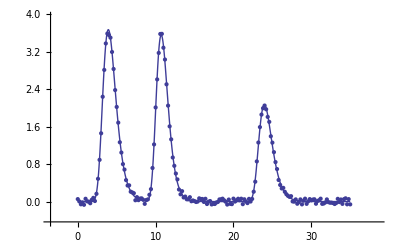

{c1→{2.,1.8},c2→{1.3,2.4},c3→{1.2,1.6},y1→{0.96,0.73},y2→{1.3,1.2},y3→{0.9,1.1},z1→{0.99,0.9},z2→{1.,1.1},z3→{1.,1.5},t1→{5.,1.},t2→{12.,1.4},t3→{25.,1.5},SumOfSquares→0.309234,DegreesOfFreedom→164}

```mathematica
EDAFindFit[mydata,c1* Galatry[y1,z1,t-t1]+c2 *Galatry[y2,z2,t-t2]+c3 *Galatry[y3,z3,t-t3],t,{{c1,1.995},{c2,1.395},{c3,1.19},{y1,0.94},{y2,1.3},{y3,0.9},{z1,1},{z2,1},{z3,1},{t1,4.9},{t2,12.1},{t3,25.1}}]
```

However, you should be aware that this fit pushed EDAFindFit pretty hard. The fit very sensitive to the initial values,  Further, many of the fitted parameters are zero within calculated errors. This is why specialized software to solve these sorts of problems has been written. See Ouyang and Varghese, listed in the references, Section 5.1.4, for an example of a technique for fitting this particular type of spectrum.

## 5.3 Options, Utilities, and Details

There are many options to EDAFindFit that control both how it does the fit and what it returns. These are discussed in Section 5.3.1.

The package also includes programs that are used by EDAFindFit, but may also be used directly. These are the topic of Section 5.3.2, which also discusses some convenience functions of various peak shapes.

First we load EDA.

```mathematica
Needs["EDA`"]
```

### 5.3.1 Options to EDAFindFit

The options and default values used directly by EDAFindFit are given by using Options.

```mathematica
TableForm[Options[EDAFindFit]]
```

AbsoluteChiSquaredTolerance→0.1
MaximumIterations→30
Method→LevenbergMarquardt
RelativeChiSquaredTolerance→0.005
ReturnCovariance→False
ReturnEffectiveVariance→False
ReturnErrors→True
ReturnFunction→False
ReturnResiduals→False
Reweight→False
ShowFit→True
EDAShowProgress→False
EDAAccuracyGoal→Automatic
EDAPrecisionGoal→Automatic
UseSignificantFigures→True
ValueTolerance→0.002

Below, we first discuss the Method option, followed by the other options to EDAFindFit in order.

In addition, if ShowFit is set to True, the default, EDAFindFit, uses the function ShowFitResult. This function is discussed in Section 5.3.2. Options to ShowFitResult given to EDAFindFit are passed to that function.

If EDAFindFit is called with ReturnFunction set to True, or if the ShowFit option is set to True (the default) the function ToFitFunction is called. This function is discussed in Section 5.4.2. Options to ToFitFunction given to EDAFindFit are passed to that function.

#### 5.3.1.0 The Method Option

In many cases, EDAFindFit by default uses the Mathematica built-in function FindMinimum with a LevenbergMarquardt method. EDAFindFit can use other methods, controlled with a Method option. Valid values include Gradient, Newton, and QuasiNewton, all of which are passed to FindMinimum.

EDAFindFit has its own Levenberg-Marquardt algorithm, coded in a form very similar to that described by Press et al. in Numerical Recipes, §14.4. When Method is set to EDALM this code will be used to find the fit. EDALM will always be used when either there are explicit errors in both coordinates of the data or when the Reweight option discussed below has been set to True, or if the model being fit to is linear; in all of these cases this behavior is invisible unless the ShowProgress option discussed below is set to True.

Here is an illustration. First we fit Cobalt60Data to a Gaussian plus linear background without reweighting; we also suppress the graphs of the fit by using the ShowFit option.

```mathematica
EDAFindFit[Cobalt60Data, a0 + a1* chan +  Gaussian[chan, ampl, x0, sigma], chan, {{a0, 194}, {a1, -0.092}, {ampl, 154}, {x0, 1833}, {sigma, 43}}, ShowFit -> False]
```

{a0→{201.5,1.6},a1→{-0.09556,0.00087},ampl→{154.03,0.17},x0→{1833.51,0.054},sigma→{43.499,0.069},SumOfSquares→23500.7,DegreesOfFreedom→281}

Now we reweight the data.

```mathematica
EDAFindFit[Cobalt60Data, a0 + a1* chan +  Gaussian[chan, ampl, x0, sigma], chan, {{a0, 194}, {a1, -0.092}, {ampl, 154}, {x0, 1833}, {sigma, 43}}, ShowFit -> False, Reweight -> True]
```

{a0→{202.,15.},a1→{-0.0956,0.008},ampl→{154.,1.6},x0→{1833.51,0.5},sigma→{43.5,0.63},PseudoErrorY→9.1451,SumOfSquares→23500.7,DegreesOfFreedom→281}

Finally, we repeat the above fit but observe its progress. The fourth line of the progress report tells us that the method has been changed.

```mathematica
EDAFindFit[Cobalt60Data, a0 + a1* chan +  Gaussian[chan, ampl, x0, sigma], chan, {{a0, 194}, {a1, -0.092}, {ampl, 154}, {x0, 1833}, {sigma, 43}}, ShowFit -> False, Reweight -> True, EDAShowProgress -> True]
```

286 data points with 2 variables.
Fitting to 5 parameters

Beginning iterations.

Warning: since the Reweight option has been turned on, the Method has been set to EDALM.

Iteration 1 Sum of squares = 24446.4 Previous sum of squares: 1.79769×10^308

Current answer: {a0→194,a1→-0.092,ampl→154,x0→1833,sigma→43}

Evaluating matrices for the current answer.

Scale for step size (lambda) = 0.001

Using singular value decomposition to find corrections.

Corrections to parameters: {3.1815,-0.00126128,0.0936646,0.439485,0.568223}

Iteration 2 Sum of squares = 23507.9 Previous sum of squares: 24446.4

Current answer: {a0→197.182,a1→-0.0932613,ampl→154.094,x0→1833.44,sigma→43.5682}

Evaluating matrices for the current answer.

Scale for step size (lambda) = 0.0001

Using singular value decomposition to find corrections.

Corrections to parameters: {3.76218,-0.00198369,-0.0493587,0.0612,-0.0644802}

Iteration 3 Sum of squares = 23500.8 Previous sum of squares: 23507.9

Current answer: {a0→200.944,a1→-0.095245,ampl→154.044,x0→1833.5,sigma→43.5037}

Convergence: the relative decrease in the sumofsquares is less than: 0.005

Reweighting the data with erry = 83.6329

Evaluating matrices for the current answer.

Scale for step size (lambda) = 0.001

Using singular value decomposition to find corrections.

Corrections to parameters: {19.4208,-0.010358,-0.315974,0.431694,-0.155316}

Iteration 4 Chi-squared = 282.617 Previous chi-squared: 23500.8

Current answer: {a0→220.365,a1→-0.105603,ampl→153.728,x0→1833.93,sigma→43.3484}

Evaluating matrices for the current answer.

Scale for step size (lambda) = 0.0001

Using singular value decomposition to find corrections.

Corrections to parameters: {-16.2564,0.00867934,0.25074,-0.371448,0.121765}

Iteration 5 Chi-squared = 281.028 Previous chi-squared: 282.617

Current answer: {a0→204.108,a1→-0.0969237,ampl→153.979,x0→1833.56,sigma→43.4702}

Evaluating matrices for the current answer.

Scale for step size (lambda) = 0.00001

Using singular value decomposition to find corrections.

Corrections to parameters: {-2.52622,0.0013394,0.0537354,-0.047238,0.0273204}

Iteration 6 Chi-squared = 280.998 Previous chi-squared: 281.028

Current answer: {a0→201.582,a1→-0.0955843,ampl→154.033,x0→1833.51,sigma→43.4975}

Convergence: the previous chisquared minus the current chisquared is less than: 0.1

Convergence: the relative decrease in the chisquared is less than: 0.005

Calculating covariance matrix using singular value decomposition.

{a0→{202.,15.},a1→{-0.0956,0.008},ampl→{154.,1.6},x0→{1833.51,0.5},sigma→{43.5,0.63},PseudoErrorY→9.1451,SumOfSquares→23500.7,DegreesOfFreedom→281}

The EDALM method is the only one which uses the following options: AbsoluteChiSquaredTolerance, MaximumIterations, RelativeChiSquaredTolerance, and ValueTolerance.

#### 5.3.1.1 The AbsoluteChiSquaredTolerance Option

When EDAFindFit is performing a fit using the EDALM algorithm discussed in Section 5.3.1.0, it uses three separate tests to determine if a fit has converged to a final value. The AbsoluteChiSquaredTolerance option is used by one of those tests.

If the chi-squared (or the sum of the squares if there are no explicit errors in the data) is decreasing and, in the current iteration, its value is less than the value in the previous iteration by AbsoluteChiSquaredTolerance, the fit is judged to have converged.

If there are declared errors in the data being fit, so that the test is comparing chi-squared statistics, the default value of 0.1 for this option is usually reasonable. If there are no declared errors, so the test is comparing the sum of the squares of the residuals, then the actual value of the sum of the squares depends on the magnitude of the values of the dependent variable. In this case some adjustment of the value of AbsoluteChiSquaredTolerance may be appropriate.

For information on the other two tests used by EDAFindFit to determine convergence, see the discussion of the RelativeChiSquaredTolerance and ValueTolerance options in 5.3.1.3 and in 5.3.1.15, respectively.

#### 5.3.1.2 The MaximumIterations Option

As discussed above, EDAFindFit uses an iterative technique to try to determine the minimum in the chi-squared or sum of the squares. The MaximumIterations option controls the number of iterations EDAFindFit will attempt before giving up.

When EDAFindFit gives up, it issues a warning message, but also presents the result of the fit just as if it had converged. For example, here we repeat a fit we performed in Section 5.1.3, but we restrict the number of iterations to less than that required by EDAFindFit to achieve convergence.

EDAFindFit::maxiters: EDAFindFit failed to converge after 2 iterations. The
	maximum number of iterations can be increased with the
	MaximumIterations option.

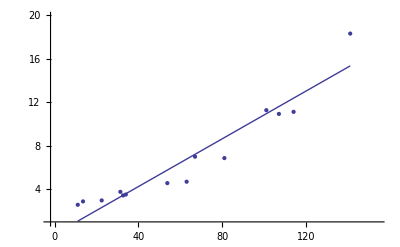

{a[0]→{-0.16,0.5},a[1]→{0.1098,0.0067},SumOfSquares→25.5589,DegreesOfFreedom→12}

```mathematica
EDAFindFit[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},MaximumIterations->2]
```

#### 5.3.1.3 The RelativeChiSquaredTolerance Option

When EDAFindFit is performing a fit using the EDALM algorithm discussed in Section 5.3.1.0, it uses three separate tests to determine if a fit has converged to a final value. The RelativeChiSquaredTolerance option is used by one of those tests.

If the chi-squared (or the sum of the squares if there are no explicit errors in the data) is decreasing, and the value of the previous iteration minus the current value divided by the previous value is less than the value of RelativeChiSquaredTolerance, then the fit is judged to have converged.

If there are declared errors, so that the test is comparing chi-squared statistics, the default value of 0.005 for this option is usually reasonable. If there are no declared errors, so the test is comparing the sum of the squares of the residuals, then the actual value of the sum of the squares depends on the magnitude of the values of the dependent variable; in this case some adjustment of the value of RelativeChiSquaredTolerance may be appropriate.

For information on the other two tests used by EDAFindFit to determinate convergence, see the discussion of the AbsoluteChiSquaredTolerance option and of the ValueTolerance option in 5.3.1.1 and in 5.3.1.15, respectively.

#### 5.3.1.4 The ReturnCovariance Option

If the ReturnCovariance option is set to True, then EDAFindFit returns the full covariance matrix of the fit in addition to other rules about the result.

A discussion of the meaning of the covariance matrix is in Section 4.4.18.

#### 5.3.1.5 The ReturnEffectiveVariance Option

When both coordinates have errors, EDAFindFit uses an “effective variance” technique. This method is discussed in Section 4.1.3.

If the ReturnEffectiveVariance option to EDAFindFit is set to True, then the program returns the values of the effective variance in addition to other rules about the result.

This option is identical to the option of the same name used by LinearFit.

#### 5.3.1.6 The ReturnErrors Option

By default, EDAFindFit calculates and returns the errors in the fit parameters. It also uses these errors to adjust the significant figures in the values of the parameters. If ReturnErrors is set to False, no errors are returned and no significant figure adjustment is performed.

For example, here we repeat a fit performed before in this chapter, one with and the other without ReturnErrors set to True. We also set ShowFit to False to suppress the graphs of the fit.

```mathematica
EDAFindFit[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},ShowFit->False]
```

{a[0]→{0.03,0.5},a[1]→{0.1068,0.0067},SumOfSquares→25.3546,DegreesOfFreedom→12}

```mathematica
EDAFindFit[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},ShowFit->False,ReturnErrors->False]
```

{a[0]→0.0309837,a[1]→0.106788,SumOfSquares→25.3546,DegreesOfFreedom→12}

This option is identical to the option of the same name used by LinearFit.

#### 5.3.1.7 The ReturnFunction Option

Be default, EDAFindFit returns a set of rules for the result of the fit. By setting ReturnFunction to True, EDAFindFit instead returns a function of the independent variable.

For example, here we repeat a fit performed a few times already in this section, but with ReturnFunction set to True. We also set ShowFit to False to suppress the graphs of the fit.

```mathematica
EDAFindFit[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},ShowFit->False,ReturnFunction->True]
```

0.03+0.1068 x

This option is identical to the option of the same name used by LinearFit.

#### 5.3.1.8 The ReturnResiduals Option

If set to True, the ReturnResiduals option causes EDAFindFit to return the residuals of the fit along with the other results of the fit.

This option is identical to the option of the same name used by LinearFit.

#### 5.3.1.9 The Reweight Option

When the data has no explicit errors, EDAFindFit finds the minimum in the sum of the squares of the residuals. However, if the scatter in the data points can be considered to be random and statistical then it is often reasonable to assume that the effective error in the dependent variable is given by PseudoErrorY.

```mathematica
PsuedoErrorY = √(SumOfSquares/DegreesOfFreedom)
```

The Reweight option is identical to the option of the same name used by LinearFit except that by default it is True for LinearFit, but False for EDAFindFit. This is because in a nonlinear fit, reweighting the data can change the values of the parameters to which we are fitting. This is not true for a linear fit, where reweighting only affects the calculated errors in those parameters.

Here is an example. ChwirutData is ultrasonic calibration data.

```mathematica
?ChwirutData
```

ChwirutData is data on ultrasonic calibration, taken by Daniel Chwirut
	in the 1970s at the National Institutes of Standards and
	Technology (NIST) in the U.S.A. The data format is {d, r}, where d
	is the metal distance and r is the ultrasonic response. The dataset
	is now part of the Statistical Reference Datasets (StRD) maintained
	by NIST at www.nist.gov/itl/div898/strd, where it is identified
	as "chwirut2."

The data can be fit to:

```mathematica
ⅇ^(-b1 x)/(b2+b3 x)
```

and the “certified” values of the parameters are:

```mathematica
b1 -> {1.6657666537E-01, 3.8303286810E-02}, b2 -> {5.1653291286E-03, 6.6621605126E-04}, 
b3 -> {1.2150007096E-02, 1.5304234767E-03}
```

Here are the results of fitting the data.

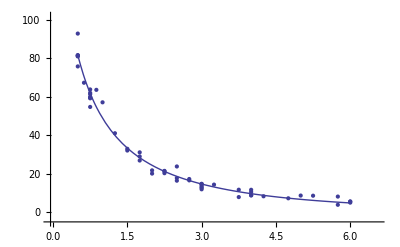

{b1→{0.167,0.012},b2→{0.00517,0.00021},b3→{0.01215,0.00048},SumOfSquares→513.048,DegreesOfFreedom→51}

```mathematica
EDAFindFit[ ChwirutData, Exp[-b1*x]/(b2 + b3*x), x, {{b1, 0.1}, {b2, 0.01}, {b3, 0.02}}]
```

Although the values of the parameters from the fit are close to the certified values, the errors are quite different from the certified values. Turning on reweighting makes the errors close to the certified values.

```mathematica
EDAFindFit[ ChwirutData, Exp[-b1*x]/(b2 + b3*x), x, {{b1, 0.1}, {b2, 0.01}, {b3, 0.02}}, Reweight -> True, ShowFit -> False]
```

{b1→{0.167,0.038},b2→{0.00517,0.00067},b3→{0.0121,0.0015},PseudoErrorY→3.17171,SumOfSquares→513.048,DegreesOfFreedom→51}

You may wish to know that Mathematica supplies nonlinear fitters, such as NonlinearModelFit, which use reweighting by default and are optimized for those types of fits. EDA’s EDAFindFit is optimized for the case when explicit errors are given in one or both coordinates of the data.

#### 5.3.1.10 The ShowFit Option

Setting ShowFit to False suppresses the display of the graphical information about the fit. As discussed in Section 5.3.2.1, the graphs can be created later from the result returned by EDAFindFit.

This option is identical to the option of the same name used by LinearFit.

#### 5.3.1.11 The EDAShowProgress Option

Setting EDAShowProgress to True causes EDAFindFit to print information about its progress in performing the fit. This option is identical to the one of the same name used by LinearFit, although for EDAFindFit the information is much more verbose and more often of use in finding the “best” fit of the data to a model.

Here we repeat a fit done a few times already in this section, setting ShowProgress to True and setting ShowFit to False to suppress the graphs of the fit.

```mathematica
EDAFindFit[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},ShowFit->False,EDAShowProgress->True]
```

14 data points with 2 variables.
Fitting to 2 parameters

Warning: the model appears to be linear. Setting the Method to EDALM.

Beginning iterations.

Iteration 1 Sum of squares = 62556.7 Previous sum of squares: 1.79769×10^308

Current answer: {a[0]→1,a[1]→1}

Evaluating matrices for the current answer.

Scale for step size (lambda) = 0.001

Using singular value decomposition to find corrections.

Corrections to parameters: {-1.15781,-0.890167}

Iteration 2 Sum of squares = 25.5589 Previous sum of squares: 62556.7

Current answer: {a[0]→-0.15781,a[1]→0.109833}

Evaluating matrices for the current answer.

Scale for step size (lambda) = 0.0001

Using singular value decomposition to find corrections.

Corrections to parameters: {0.188662,-0.00304403}

Iteration 3 Sum of squares = 25.3546 Previous sum of squares: 25.5589

Current answer: {a[0]→0.0308523,a[1]→0.106789}

Evaluating matrices for the current answer.

Scale for step size (lambda) = 0.00001

Using singular value decomposition to find corrections.

Corrections to parameters: {0.000131454,-1.80534×10^-6}

Iteration 4 Sum of squares = 25.3546 Previous sum of squares: 25.3546

Current answer: {a[0]→0.0309837,a[1]→0.106788}

Convergence: the previous sumofsquares minus the current sumofsquares is less than: 0.1

Convergence: the relative decrease in the sumofsquares is less than: 0.005

Calculating covariance matrix using singular value decomposition.

{a[0]→{0.03,0.5},a[1]→{0.1068,0.0067},SumOfSquares→25.3546,DegreesOfFreedom→12}

Note that the final iteration satisfied two of the three possible criteria for convergence. This is common when EDAFindFit has found a true minimum in the sum of the squares.

#### 5.3.1.12 The EDAAccuracyGoal Option

As discussed above, in many cases EDAFindFit uses the Mathematica built-in FindMinimum. For these cases EDAAccuracyGoal is passed to FindMinimum as the AccuracyGoal.

#### 5.3.1.13 The EDAPrecisionGoal Option

As discussed above, in many cases EDAFindFit uses the Mathematica built-in FindMinimum. For these cases EDAPrecisionGoal is passed to FindMinimum as the PrecisionGoal.

#### 5.3.1.14 The UseSignificantFigures Option

As discussed in Chapter 3, in the physical sciences specifying the error associated with a quantity essentially defines what the significant figures of that quantity are. By default, EDAFindFit uses this definition of significant figures in returning the value of fit parameters. The UseSignificantFigures option allows this default behavior to be turned off. For example, here we repeat a fit we have already done a few times.

```mathematica
EDAFindFit[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},ShowFit->False]
```

{a[0]→{0.03,0.5},a[1]→{0.1068,0.0067},SumOfSquares→25.3546,DegreesOfFreedom→12}

```mathematica
EDAFindFit[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},ShowFit->False,UseSignificantFigures->False]
```

{a[0]→{0.0309837,0.498084},a[1]→{0.106788,0.00673957},SumOfSquares→25.3546,DegreesOfFreedom→12}

Now the estimated errors in the fitted parameters have not been used to adjust the number of significant figures displayed for either the values or the errors in those parameters.

In Section 5.3.1.9 above, we were comparing a fit to ChwirutData to “certified values.” The fit result was as follows.

```mathematica
EDAFindFit[ ChwirutData, Exp[-b1*x]/(b2 + b3*x), x, {{b1, 0.1}, {b2, 0.01}, {b3, 0.02}}, Reweight -> True, ShowFit -> False]
```

{b1→{0.167,0.038},b2→{0.00517,0.00067},b3→{0.0121,0.0015},PseudoErrorY→3.17171,SumOfSquares→513.048,DegreesOfFreedom→51}

The certified values are:

```mathematica
b1 -> {1.6657666537E-01, 3.8303286810E-02}, b2 -> {5.1653291286E-03, 6.6621605126E-04}, 
b3 -> {1.2150007096E-02, 1.5304234767E-03}
```

Turning off significant figure adjustment allows us to compare the result of EDAFindFit to the certified values more carefully.

```mathematica
EDAFindFit[ ChwirutData, Exp[-b1*x]/(b2 + b3*x), x, {{b1, 0.1}, {b2, 0.01}, {b3, 0.02}}, Reweight -> True, ShowFit -> False, UseSignificantFigures -> False]
```

{b1→{0.166667,0.0384618},b2→{0.00516669,0.00066543},b3→{0.0121465,0.00153031},PseudoErrorY→3.17171,SumOfSquares→513.048,DegreesOfFreedom→51}

This UseSignificantFigures option is identical to the option of the same name used by LinearFit.

#### 5.3.1.15 The ValueTolerance Option

When EDAFindFit is performing a fit using the EDALM algorithm discussed in Section 5.3.1.0, it uses three separate tests to determine if a fit has converged to a final value. The ValueTolerance option is used by one of those tests.

If the chi-squared or sum of the squares is decreasing, and the maximum of the absolute value of the change in the fit parameters is less than ValueTolerance, the fit is judged to have converged. The default value is 0.002.

For information on the other two tests used by EDAFindFit to determinate convergence, see the discussion of the AbsoluteChiSquaredTolerance and RelativeChiSquaredTolerance option in Section 5.3.1.1 and Section 5.3.1.3, respectively.

### 5.3.2 Other Routines in the EDAFindFit Package

#### 5.3.2.1 The ShowFitResult Routine

By default EDAFindFit uses the program ShowFitResult to display the results of a fit. If we have the results of EDAFindFit, we can use ShowFitResult to display it. We will demonstrate with GanglionData as used above.

```mathematica
result=EDAFindFit[GanglionData,a[0]+a[1] x+a[2] x^2,x,{a[0],a[1],a[2]},ShowFit->False]
```

{a[0]→{2.91,0.82},a[1]→{-0.013,0.028},a[2]→{0.00084,0.00019},SumOfSquares→5.52066,DegreesOfFreedom→11}

Now we display the results of the fit.

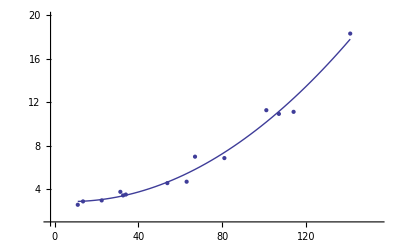

```mathematica
ShowFitResult[GanglionData,a[0]+a[1] x+a[2] x^2,x,{a[0],a[1],a[2]},result]
```

Note that ShowFitResult returns a Graphics object. This can be convenient if you wish to print the graphic, since the Graphics object is not returned by EDAFindFit itself.

Note that the syntax and functionality of ShowFitResult are very similar to that of ShowLinearFit in the EDA`LinearFit` package.

By default, ShowFitResult tries to find a quadrant in the data-fit graph in which to place the residual plot. If no such quadrant can be found, the residual plot is displayed separately. Setting ResidualPlacement to Separate causes the residual plot to always be displayed separately. ResidualPlacement can also be set to an integer between 1 and 4, which causes the residual plot to be placed in that quadrant of the data-fit plot.

```mathematica
ShowFitResult[GanglionData,a[0]+a[1] x+a[2] x^2,x,{a[0],a[1],a[2]},result,ResidualPlacement->4]
```

-Graphics-

If ResidualPlacement is set to None, no residual plot is displayed.

By default, the plot of the fit results only spans the values of the data. An Extrapolate option causes the values of the independent variable to be in the range specified by the option.

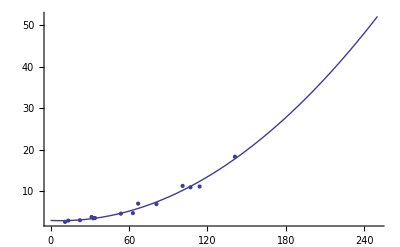

```mathematica
ShowFitResult[GanglionData,a[0]+a[1] x+a[2] x^2,x,{a[0],a[1],a[2]},result, Extrapolate -> {0, 250}]
```

Internally, ShowFitResult uses EDAListPlot, Plot, and ToFitFunction. Options given to ShowFitResult for these are passed to the appropriate program. In addition, ShowFitResult itself uses only the two options ResidualPlacement and UseSignificantFigures.

There can be some minor differences between the graphs displayed by EDAFindFit and those displayed by ShowFitResult. For example, if the data set has no explicit errors and the Reweight option is set to True in the call to EDAFindFit, then the PseudoErrorY is used in the calculation of the errors in the residuals by EDAFindFit. ShowFitResult is unaware of this, and will then have slightly different errors in the residual graph. By specifying ReturnResiduals to True in the call to EDAFindFit, the “better” numbers will be used by ShowFitResult.

We give an example by fitting GanglionData with the Reweight option.

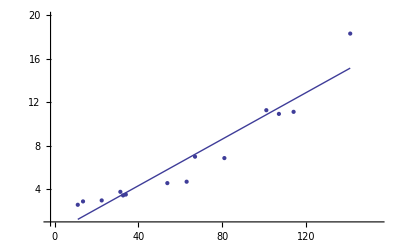

{a[0]→{0.03,0.72},a[1]→{0.107,0.01},PseudoErrorY→1.45358,SumOfSquares→25.3546,DegreesOfFreedom→12}

```mathematica
result=EDAFindFit[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},Reweight->True,ShowFit->True]
```

Next we use ShowFitResult on result.

```mathematica
ShowFitResult[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},result]
```

-Graphics-

ShowLinearFit does not show the errors in the residuals due to the PseudoErrorY term.

We can have EDAFindFit explicitly return the residuals.

```mathematica
result=EDAFindFit[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},Reweight->True,ShowFit->False,ReturnResiduals->True]
```

{a[0]→{0.03,0.72},a[1]→{0.107,0.01},Residuals→{{11.1,{1.3,1.5}},{13.6,{1.4,1.5}},{22.5,{0.5,1.5}},{31.4,{0.4,1.5}},{32.7,{-0.1,1.5}},{34.,{-0.2,1.5}},{53.8,{-1.2,1.5}},{63.,{-2.1,1.5}},{67.,{-0.2,1.5}},{81.,{-1.8,1.5}},{101.,{0.4,1.5}},{107.,{-0.5,1.5}},{114.,{-1.1,1.5}},{141.,{3.2,1.5}}},PseudoErrorY→1.45358,SumOfSquares→25.3546,DegreesOfFreedom→12}

We see that the PseudoErrorY has led to an error in each of the residuals. ShowFitResult will display these in this case.

```mathematica
ShowFitResult[GanglionData,a[0]+a[1] x,x,{a[0],a[1]},result]
```

-Graphics-

Similarly, if the data set has errors in both coordinates, EDAFindFit uses the effective variance in calculating the errors in the residuals. In this case also, specifying ReturnResiduals as True in the call to EDAFindFit will cause ShowFitResult to be slightly more correct.

#### 5.3.2.2 The ToFitFunction Routine

ShowFitResult, discussed previously, uses the function ToFitFunction to graph the results of the fit. EDAFindFit also directly calls ToFitFunction if the option ReturnFunction is set to True.

The function may also be called directly. We repeat a fit we have done before.

```mathematica
result=EDAFindFit[ThermocoupleData,a[0]+a[1] x,x,{a[0],a[1]},ShowFit->False]
```

{a[0]→{-0.981,0.021},a[1]→{0.04122,0.00036},ChiSquared→21.0535,DegreesOfFreedom→19}

We pass the result to ToFitFunction.

```mathematica
ToFitFunction[result,a[0]+a[1] x,x,{a[0],a[1]}]
```

-0.981+0.04122 x

ToFitFunction is similar to the ToLinearFunction function supplied in the EDA`LinearFit` package, but somewhat more general. One difference is that when the fit parameters have errors, by default ToFitFunction does not return two functions. In contrast, ToLinearFunction will return two functions, the first being the result of the fit and the second the estimated errors in the function. ToFitFunction can return this second “error function” if the UseFitErrors option is set to True.

```mathematica
ToFitFunction[result,a[0]+a[1] x,x,{a[0],a[1]},UseFitErrors->True]
```

{-0.981+0.04122 x,√(0.000441+1.296×10^-7 x^2)}

### 5.3.3 Peak Shape Routines

The EDA`FindFit` package includes some convenience functions to define peak shapes. They are BreitWigner, Galatry, Gaussian, Lorentzian, PearsonVII, RelativisticBreitWigner, and Voigt.

## 5.4 Summary of the EDAFindFit Package

```mathematica
Needs["EDA`"]
```

```mathematica
Information["EDAFindFit",LongForm->False]
```

EDAFindFit[data, model, ind, parameters] finds a fit of "data" to
	"model" that minimizes the sum of the squares of the residuals or the
	chi-squared. The model is expected to be a function of the independent
	variable "ind" and the variables named in "parameters". The parameters
	can be of the form {name1, name2, ... , nameM}, but will more usually
	be of the form { {name1, start1}, {name2, start2}, ... , {nameM, startM}},
	where "starti" is initial values of the parameter. In addition, each
	parameter can be specified as {name, min, start, max}, where "name" is
	the name, "start" is the starting value, and "min" and "max" specify
	the minimum and maximum values of the parameter that can be returned.
	Finally, the parameter can be specified as {name, min, max} in which
	case the starting value is (min + max)/2. By default, EDAFindFit uses
	the Levenberg-Marquardt algorithm. If there are no declared errors
	in the independent variable, other methods, chosen with a
	Method option, can be EDALM, Gradient, Newton, or QuasiNewton.

```mathematica
Information["AbsoluteChiSquaredTolerance",LongForm->False]
```

AbsoluteChiSquaredTolerance is used in the default convergence
	test of EDAFindFit. When the chi-squared of the current iteration
	is less than the chi-squared of the previous iteration and their
	difference is less than AbsoluteChiSquaredTolerance, the fit is
	judged to have converged and no more iterations are performed.

```mathematica
Information["MaximumIterations",LongForm->False]
```

MaximumIterations is an option for various routines that use	iterative techniques. It specifies the maximum number
	of iterations to perform before quitting.

```mathematica
Information["RelativeChiSquaredTolerance",LongForm->False]
```

RelativeChiSquaredTolerance is used in the default convergence
	test of EDAFindFit. When the chi-squared of the current iteration
	is less than the chi-squared of the previous iteration and their
	relative difference is less than RelativeChiSquaredTolerance, the fit
	is judged to have converged and no more iterations are performed.

```mathematica
Information["ReturnCovariance",LongForm->False]
```

ReturnCovariance is an option for various fitting routines.
	If set to True, then the routine returns the full covariance matrix.	Otherwise, it does not.

```mathematica
Information["ReturnEffectiveVariance",LongForm->False]
```

ReturnEffectiveVariance is an option for various fitting routines.	If set to True, the routine returns the effective variance as part of	the result of the fit.

```mathematica
Information["ReturnErrors",LongForm->False]
```

ReturnErrors is an option for various fitting routines. If set to	True, then the routine returns errors in the fitted parameters.	Otherwise, it does not.

```mathematica
Information["ReturnFunction",LongForm->False]
```

ReturnFunction is an option for various fitting routines. If
	set to False, then the fit will be returned as a set of rules	involving the "parameter" given in the call to the routine.
	If set to True, then the fit will be returned as a function
	and the independent variable is taken to be "parameter".

```mathematica
Information["ReturnResiduals",LongForm->False]
```

ReturnResiduals is an option for various fitting routines. If
	set to True, the residuals of the fit are returned along with other
	information about the fit. The residuals returned always include
	a value for the independent variable. If none is in the data, the
	values are {1, 2, ... , N}.

```mathematica
Information["Reweight",LongForm->False]
```

Reweight is an option for LinearFit and EDAFindFit, which controls
	whether or not to re-weight the data if it contains no explicit
	errors. The default is True for LinearFit and False for EDAFindFit.
	If set to True, the data is weighted using a "statistical assumption",
	where the error in the dependent variables is the square root of
	the sum of the squares divided by the number of degrees of freedom.
	See Taylor, "An Introduction to Error Analysis," Eqn 8.14 on pg.
	158 for further information. When set to True, all subsequent
	processing assumes that the generated errors in the dependent
	variable are real.

```mathematica
Information["ShowFit",LongForm->False]
```

ShowFit is an option for various fitting routines. If set to True,
	then a graphical display of the results of the fit is displayed.

```mathematica
Information["EDAShowProgress",LongForm->False]
```

EDAShowProgress is an option for various routines. When set to True, the
	routine will print messages showing its progress in performing
	its tasks. If set to False, no such information is printed.

```mathematica
Information["EDAAccuracyGoal", LongForm -> False]
```

When EDAFindFit fits to data with no errors in the independent
	coordinate and the Reweight option is False, by default the fit is
	performed by the Mathematica built-in FindMinimum. EDAAccuracyGoal
	is then the AccuracyGoal used by FindFit. By default,
	EDAAccuracyGoal is Automatic

```mathematica
Information["EDAPrecisionGoal", LongForm -> False]
```

When EDAFindFit fits to data with no errors in the independent
	coordinate and the Reweight option is False, by default the fit is
	performed by the Mathematica built-in FindMinimum. EDAPrecisionGoal
	is then the PrecisionGoal used by FindFit. By default,
	EDAPrecisionGoal is Automatic

```mathematica
Information["UseSignificantFigures",LongForm->False]
```

UseSignificantFigures is an option for various routines. When set to
	True, the routine will use AdjustSignificantFigures on numbers with
	associated errors, so that the error determines the number of
	significant figures in the number itself. If set to False, no
	such adjustment is performed.

```mathematica
Information["ValueTolerance",LongForm->False]
```

ValueTolerance is used in the default convergence test of
	EDAFindFit. When the chi-squared of the current iteration is
	less than the chi-squared of the previous iteration and the maximum
	change in the values of the parameters being fit divided by the
	value of that parameter is less than ValueTolerance, the fit is
	judged to have converged and no more iterations are performed.

```mathematica
Information["ShowFitResult",LongForm->False]
```

ShowFitResult[data, model, ind, parameters, result] takes
	results from EDAFindFit and displays graphic information
	about the fit. The meaning of the first four arguments is
	identical to arguments of the same name for EDAFindFit. Note
	that if parameters contains {param, value} pairs, the values are
	ignored by ShowFitResult. ShowFitResult[data, model, ind,
	parameters, result, residuals] is the same as the first form,
	except the residuals of the fit are given instead of calculated.

```mathematica
Information["Extrapolate", LongForm -> False]
```

Extrapolate is an option for ShowLinearFit and ShowFitResult.
	If set to False (the default), the graph of the fit results spans
	the data. If set to {xmin, xmax}, the graph of the fit results
	uses a plot range in the independent variable of {xmin, xmax}.

```mathematica
Information["ResidualPlacement",LongForm->False]
```

ResidualPlacement is an option for ShowLinearFit and ShowFitResult.
	If set to Automatic, they try to place the plot of residuals as a small
	graph inside the graph of the data and results of the fit. If
	a quadrant cannot be found, then the residual plot is displayed
	separately. If the option is set to Separate, then the residual
	plot is always displayed separately. If the option is set to
	an integer between 1 and 4, that quadrant is used to display
	the residuals. If the option is set to None, no residuals
	are displayed.

```mathematica
Information["ToFitFunction",LongForm->False]
```

ToFitFunction[result, model, ind, parameters] takes a result,
	which is assumed to be a set of rules such as is returned by
	default by EDAFindFit, and returns a function of the independent
	variable "ind" for "model". The model is assumed to be a function
	of "ind" and the "parameters". The "parameters" may be a list of
	symbols, or {symbol, value} pairs, although the values are ignored
	in all cases. By default, a single function is returned, which
	is evaluated at the result of the fit. If UseFitErrors is set
	to True, the routine returns a list of two functions. The first
	is as before and the second is the estimated error in the function
	due to the errors in the fit parameters, if any.

```mathematica
Information["UseFitErrors",LongForm->False]
```

UseFitErrors is an option for ToLinearFunction and ToFitFunction.
	If set to True (the default for ToLinearFunction) and the result
	contains errors in the fitted parameters, then two functions are
	returned. The first is the function for the values of the parameters
	and the second is the function for the values of the errors in the
	parameters. A heuristic method is used to choose the sign of each
	term in the function of the errors in the parameters. If UseFitErrors
	is set to False (the default for ToFitFunction), only a single function
	evaluated at the values of the parameters is used.

```mathematica
Information["BreitWigner",LongForm->False]
```

BreitWigner[x, a, x0, gamma] is a nonrelativistic Breit-Wigner
	function of the independent variable x, center value x0, and full
	width at half-maximum gamma. The function is normalized
	so that its integral from -Infinity to +Infinity is equal to 
	"a". The maximum amplitude of the peak is 2*a/(Pi*gamma). BreitWigner
	is a synonym for Lorentzian.

```mathematica
Information["Galatry",LongForm->False]
```

Galatry[y, z, tau] is a Galatry profile with collision broadening
	parameter "y", collision narrowing parameter "z", and dimensionless
	time "tau". The profile is normalized so that its value is one
	when tau = 0.

```mathematica
Information["Lorentzian",LongForm->False]
```

Lorentzian[x, a, x0, gamma] is a nonrelativistic Lorentzian
	function of the independent variable x, center value x0, and full
	width at half-maximum gamma. The function is normalized
	so that its integral from -Infinity to +Infinity is equal to 
	"a". The maximum amplitude of the peak is 2*a/(Pi*gamma). Lorentzian
	is a synonym for BreitWigner.

```mathematica
Information["PearsonVII",LongForm->False]
```

PearsonVII[x, a, x0, gamma, m] is a Pearson VII function of the independent
	variable x, absorbance a, center value x0, full width at half
	maximum gamma, and tailing factor m.

```mathematica
Information["RelativisticBreitWigner",LongForm->False]
```

RelativisticBreitWigner[m_, mr_, gamma_, m1_, m2_] generates a
	relativistic Breit-Wigner for a resonance of nominal mass mr and total
	width gamma decaying into two particles of rest mass m1 and m2. It
	returns the fraction of such decays whose invariant mass is m. The
	function is normalized so that when m equals mr, the function returns
	1.

```mathematica
Information["Voigt",LongForm->False]
```

Voigt[y, tau] is a Voigt profile with collision broadening parameter
	"y" and dimensionless time "tau". The profile is Limit[ Galatry[
	y, z, tau], z -> 0].